# Hamiltonian Evolution for Three Site Rotations

```mathematica
s0 = ({{1, 0}, {0, 1}});
sx = ({{0, 1}, {1, 0}});
sy = ({{0, -ⅈ}, {ⅈ, 0}});
sz=({{1, 0}, {0, -1}});
I0[L_]:=Block[{xtp,ltp,i},
ltp = Table[s0,{i,1,L}];
xtp = ltp[[1]];
For[i=2,i≤L,i++,
xtp=KroneckerProduct[ltp[[i]],xtp];
];

xtp
];
X[l_,L_]:=Block[{xtp,ltp,i},
ltp = Table[s0,{i,1,L}];
ltp[[l]]=sx;
xtp = ltp[[1]];
For[i=2,i≤L,i++,
xtp=KroneckerProduct[ltp[[i]],xtp];
];

xtp
];

Y[l_,L_]:=Block[{xtp,ltp,i},
ltp = Table[s0,{i,1,L}];
ltp[[l]]=sy;
xtp = ltp[[1]];
For[i=2,i≤L,i++,
xtp=KroneckerProduct[ltp[[i]],xtp];
];

xtp
];

Z[l_,L_]:=Block[{xtp,ltp,i},
ltp = Table[s0,{i,1,L}];
ltp[[l]]=sz;
xtp = ltp[[1]];
For[i=2,i≤L,i++,
xtp=KroneckerProduct[ltp[[i]],xtp];
];

xtp
];
X1 = X[1,3];
Y1 = Y[1,3];
Z1 = Z[1,3];
X2 = X[2,3];
Y2 = Y[2,3];
Z2 = Z[2,3];
X3 = X[3,3];
Y3 = Y[3,3];
Z3 = Z[3,3];
```

## From the initial Hamiltonian

```mathematica
H[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{htp, Ω1,ωr1,ϕ1, Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];

htp = 1/2 ω1 Z1+1/2 ω2 Z2+1/2 ω3 Z3+Ω1 Cos[ωr1 t +ϕ1] X1+Ω2 Cos[ωr2 t +ϕ2]X2+Ω3 Cos[ωr3 t +ϕ3]X3+1/2 ω12 X1.X2+1/2 ω23 X2.X3+1/2 ω31 X3.X1+Λ X1.X2.X3;

htp
];
```

```mathematica
ωl={0.5,0.4,0.3};
ω2l={0.1,0.15,0.07};
Ωl={0.04,0.7,0.4};
ωrl={0.4,0.6,0.3};
ϕl={0.5,0.9,0.22};
t=6;
Λ=0.01;
h=H[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
```

```mathematica
U[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{utp,ti,ut,ht,et,ψt},
utp=I0[3];
ht=H[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
{et,ψt}=Eigensystem[ht];
utp =Conjugate[Transpose[ψt]].DiagonalMatrix[ⅇ^(ⅈ et dt)].ψt;

utp
];
```

```mathematica
ψT[ψ0_,ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{ψtp,ti,ut,ht,et,ψt},
ψtp=ψ0;
For[ti=dt,ti≤t,ti+=dt,
ut =U[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt];
ψtp = ut.ψtp;
];
ψtp
];
```

```mathematica
ψ000=Table[0,{i,1,8}];
ψ000[[1]]=1;
```

```mathematica
ωl={0.5,0.4,0.3};
ω2l={0.1,0.15,0.07};
Ωl={0.04,0.7,0.4};
ωrl={0.4,0.6,0.3};
ϕl={0.5,0.9,0.22};
t=6;
Λ=0.01;
dt = 0.01;
ψt = ψT[ψ000,ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt];
```

```mathematica
ψt
```

{-0.0245885+0.275714 ⅈ,-0.0770225-0.220416 ⅈ,0.00936651-0.499661 ⅈ,0.0440443+0.107569 ⅈ,-0.0455779-0.652674 ⅈ,0.0523989+0.151471 ⅈ,0.0176517+0.381724 ⅈ,-0.0134135-0.0751406 ⅈ}

## After rotations

```mathematica
Hr[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{htp,h12,h23,h31,h123,Ω1,ωr1,ϕ1,Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31,ζ1,ζ2,ζ3,η1,η2,η3},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];
ζ1=ArcTan[(ω1-ωr1)/Ω1];    ζ2=ArcTan[(ω2-ωr2)/Ω2];    ζ3=ArcTan[(ω3-ωr3)/Ω3];  
η1=√((ω1-ωr1)^2+Ω1^2);  η2=√((ω2-ωr2)^2+Ω2^2); η3=√((ω3-ωr3)^2+Ω3^2);
h12=1/2 ω12( Cos[t ωr1+ϕ1]( Cos[ζ1]X1- (Cos[η1 t]Z1+  Sin[η1 t]Y1)Sin[ζ1] ) - Sin[t ωr1+ϕ1](Cos[η1 t]Y1-Sin[η1 t]Z1)).( Cos[t ωr2+ϕ2]( Cos[ζ2]X2- (Cos[η2 t]Z2+  Sin[η2 t]Y2)Sin[ζ2] ) - Sin[t ωr2+ϕ2](Cos[η2 t]Y2-Sin[η2 t]Z2));
h23=1/2 ω23 ( Cos[t ωr2+ϕ2]( Cos[ζ2]X2- (Cos[η2 t]Z2+  Sin[η2 t]Y2)Sin[ζ2] ) - Sin[t ωr2+ϕ2](Cos[η2 t]Y2-Sin[η2 t]Z2)).( Cos[t ωr3+ϕ3]( Cos[ζ3]X3- (Cos[η3 t]Z3+  Sin[η3 t]Y3)Sin[ζ3] ) - Sin[t ωr3+ϕ3](Cos[η3 t]Y3-Sin[η3 t]Z3));
h31=1/2 ω31 ( Cos[t ωr3+ϕ3]( Cos[ζ3]X3- (Cos[η3 t]Z3+  Sin[η3 t]Y3)Sin[ζ3] ) - Sin[t ωr3+ϕ3](Cos[η3 t]Y3-Sin[η3 t]Z3)).( Cos[t ωr1+ϕ1]( Cos[ζ1]X1- (Cos[η1 t]Z1+  Sin[η1 t]Y1)Sin[ζ1] ) - Sin[t ωr1+ϕ1](Cos[η1 t]Y1-Sin[η1 t]Z1));
h123=Λ ( Cos[t ωr1+ϕ1]( Cos[ζ1]X1- Sin[ζ1]( Cos[η1 t]I0[3].Z1+ Sin[η1 t]Y1))- Sin[t ωr1+ϕ1]( Cos[η1 t]Y1- Sin[η1 t]Z1)).( Cos[t ωr2+ϕ2]( Cos[ζ2]X2- Sin[ζ2]( Cos[η2 t]Z2+Sin[η2 t]Y2))-Sin[t ωr2+ϕ2]( Cos[η2 t]Y2- Sin[η2 t]Z2)).( Cos[t ωr3+ϕ3]( Cos[ζ3]X3- Sin[ζ3]( Cos[η3 t]Z3+ Sin[η3 t]Y3))- Sin[t ωr3+ϕ3]( Cos[η3 t]Y3-Sin[η3 t]Z3));

htp = h12+h23+h31+h123;

htp
];
```

We have to be careful when doing time evolution in this new basis since the basis is time dependent.  However, we already took care of the trick part when subtracting the unitary derivative during the transformation.  Let us see why that works.

ψ(t) = ... e^(ⅈ H(t_2)dt)e^(ⅈ H(t_1)dt)ψ(0)

U_n^t ψ(t) = U_n^t... e^(ⅈ H(t_2)dt)e^(ⅈ H(t_1)dt)ψ(0) = U_n^t... U_2 U_2^t e^(ⅈ H(t_2)dt)U_2U_2^tU_1 U_1^te^(ⅈ H(t_1)dt)U_1 U_1^tU_0 U_0^tψ(0)

				U_i^t U_(i-1) = U_i^t(U_i-dt  dU_i/dt) = 1-dt U_i^tdU_i/dt = e^(-dt U_i^t dU_i/dt)
				
U_n^t ψ(t) =  ... e^(ⅈ  (U_2^t H(t_2) U_2+i U_2^t dU_2/dt)dt)e^(ⅈ (U_1^t H(t_1)U_1+i U_1^t dU_1/dt)dt)U_0^tψ(0)

which is exactly how the Hamiltonians where transformed.  We just have to remember to transform the initial wavefunction and then transform it back.

```mathematica
Ur[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{utp,ti,ut,ht,et,ψt},
utp=I0[3];
ht=Hr[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
{et,ψt}=Eigensystem[ht];
utp =Conjugate[Transpose[ψt]].DiagonalMatrix[ⅇ^(ⅈ et dt)].ψt;

utp
];
```

```mathematica
R[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{rtp,ua,uc,ud,Ω1,ωr1,ϕ1,Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31,ζ1,ζ2,ζ3,η1,η2,η3},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];
ζ1=ArcTan[(ω1-ωr1)/Ω1];    ζ2=ArcTan[(ω2-ωr2)/Ω2];    ζ3=ArcTan[(ω3-ωr3)/Ω3];  
η1=√((ω1-ωr1)^2+Ω1^2);  η2=√((ω2-ωr2)^2+Ω2^2); η3=√((ω3-ωr3)^2+Ω3^2);

ua = (Cos[(ωr1 t+ϕ1)/2]I0[3]-ⅈ Sin[(ωr1 t +ϕ1)/2]Z1).(Cos[(ωr2 t+ϕ2)/2]I0[3]-ⅈ Sin[(ωr2 t +ϕ2)/2]Z2).(Cos[(ωr3 t+ϕ3)/2]I0[3]-ⅈ Sin[(ωr3 t +ϕ3)/2]Z3);

uc=(Cos[ζ1/2]I0[3]+ⅈ Sin[ζ1/2]Y1).(Cos[ζ2/2]I0[3]+ⅈ Sin[ζ2/2]Y2).(Cos[ζ3/2]I0[3]+ⅈ Sin[ζ3/2]Y3);

ud=(Cos[η1/2]I0[3]-ⅈ Sin[η1/2]X1).(Cos[η2/2]I0[3]-ⅈ Sin[η2/2]X2).(Cos[η3/2]I0[3]-ⅈ Sin[η3/2]X3);

rtp = ud.uc.ua;


rtp
];
```

```mathematica
ψRT[ψ0_,ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{ψtp,ti,ut,ht,et,ψt},
ψtp=R[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t].ψ0;
For[ti=dt,ti≤t,ti+=dt,
ht=Hr[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
{et,ψt}=Eigensystem[ht];
ut =Ur[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt];
ψtp = ut.ψtp;
];
ψtp =Conjugate[Transpose[ R[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t]]].ψtp;
ψtp
];
```

```mathematica
ωl={0.5,0.4,0.3};
ω2l={0.1,0.15,0.07};
Ωl={0.04,0.7,0.4};
ωrl={0.4,0.6,0.3};
ϕl={0.5,0.9,0.22};
t=0.5;
Λ=0.01;
dt = 0.001;
ψt = ψT[ψ000,ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt];
ψrt = ψRT[ψ000,ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt];
```

```mathematica
ψt
```

{0.929566-0.288705 ⅈ,-0.00904193-0.0135245 ⅈ,-0.0320955-0.120465 ⅈ,-0.00524529-0.0233898 ⅈ,-0.0461825-0.178305 ⅈ,-0.00599293-0.0158427 ⅈ,-0.0283044-0.033032 ⅈ,-0.00728142-0.00420097 ⅈ}

```mathematica
ψrt
```

{0.998849-0.00280958 ⅈ,-0.00382988-0.000290527 ⅈ,0.00101636+0.0158472 ⅈ,0.0205812-0.0000706921 ⅈ,0.000535174+0.0140874 ⅈ,0.0141641+0.0000863233 ⅈ,-0.00222706-0.0343737 ⅈ,0.00416258+0.0000688277 ⅈ}

### I need to resolve these two. Apply R to H and see if you get Hr (i.e. Hr = R^t H R). Keep in mind that you have to use the rotating wave approximation.

## From the time averaged over η effective Hamiltonian

```mathematica
Heff[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{htp,h12,h23,h31,h123,Ω1,ωr1,ϕ1,Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31,ζ1,ζ2,ζ3},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];
ζ1=ArcTan[(ω1-ωr1)/Ω1];    ζ2=ArcTan[(ω2-ωr2)/Ω2];    ζ3=ArcTan[(ω3-ωr3)/Ω3];  
h12=1/4 ω12( Cos[t ωr1+ϕ1+t ωr2+ϕ2]+Cos[t ωr1+ϕ1-t ωr2-ϕ2])Cos[ζ2] Cos[ζ1] ( X1.X2  );
h23=1/4 ω23( Cos[t ωr2+ϕ2+t ωr3+ϕ3]+Cos[t ωr2+ϕ2-t ωr3-ϕ3])Cos[ζ3] Cos[ζ2] ( X2.X3  );
h31=1/4 ω31( Cos[t ωr3+ϕ3+t ωr1+ϕ1]+Cos[t ωr3+ϕ3-t ωr1-ϕ1])Cos[ζ1] Cos[ζ3] ( X3.X1  );
h123=1/4 Λ( Cos[t ωr1+ϕ1+t ωr2+ϕ2+t ωr3+ϕ3]+Cos[t ωr1+ϕ1+t ωr2+ϕ2-t ωr3-ϕ3]+Cos[t ωr1+ϕ1-t ωr2-ϕ2+t ωr3+ϕ3]+Cos[t ωr1+ϕ1-t ωr2-ϕ2-t ωr3-ϕ3])Cos[ζ2] Cos[ζ1]Cos[ζ3] (X3. X1.X2  );

htp = h12+h23+h31+h123;

htp
];
```

### A quick look at the effective coupling strength.

The width of the peak increases with the drive strength.

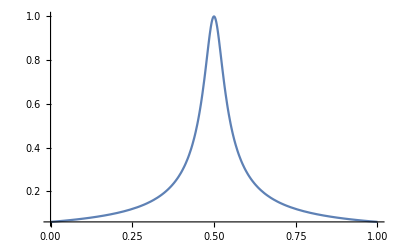

```mathematica
ζ[ω_,Ω_,ωr_]:=ArcTan[(ω-ωr)/Ω];
Plot[Cos[ζ[0.5,0.03,ωr]],{ωr,0,1},PlotRange->All]
```

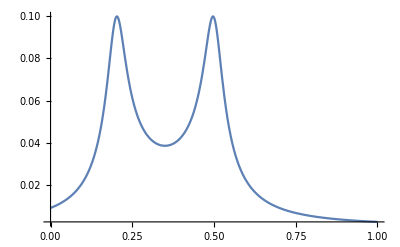

```mathematica
Plot[Cos[ζ[0.5,0.03,ωr]] Cos[ζ[0.2,0.03,ωr]],{ωr,0,1},PlotRange->All]
```

### Return to the time evolution